```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2"];
```

```mathematica
d1=T[Import["ksamples1.csv"]][[;;,2;;]];
d2=T[Import["ksamples2.csv"]][[;;,2;;]];
d3=T[Import["ksamples3.csv"]][[;;,2;;]];
```

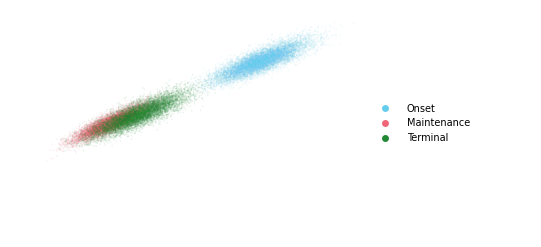

```mathematica
plot=ListPlot[{d1[[;;,{2,3}]],d2[[;;,{2,3}]],d3[[;;,{2,3}]]},Joined->False,PlotStyle->Opacity[0.1],PlotLegends->mylegendsc[{blue,red,green},{"Onset","Maintenance","Terminal"},Top],FrameLabel->{"difference of histogram means","difference of histogram variances"},ImageSize->a4longside]
```

```mathematica
Export["anxiety_vs_insomnia_means.png",plot,Magnification->1]
```

anxiety_vs_insomnia_means.png

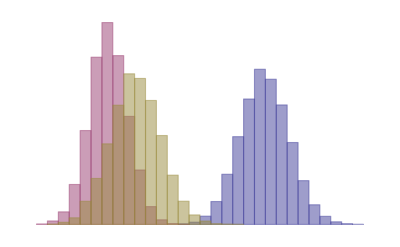

```mathematica
Histogram[{d1[[;;,1]],d2[[;;,1]],d3[[;;,1]]},"FreedmanDiaconis","PDF",ChartStyle->Opacity[0.5]]
```

```mathematica
Histogram[{d1[[;;,2]],d2[[;;,2]],d3[[;;,2]]},"FreedmanDiaconis","PDF",ChartStyle->Opacity[0.5]]
```

-Graphics-

```mathematica
d1[[;;30,{1,2}]]
```

{{0.41392,0.41392},{0.400983,0.400983},{0.399091,0.399091},{0.396163,0.396163},{0.414592,0.414592},{0.405978,0.405978},{0.354101,0.354101},{0.389542,0.389542},{0.440225,0.440225},{0.387462,0.387462},{0.368016,0.368016},{0.397058,0.397058},{0.386369,0.386369},{0.37659,0.37659},{0.404274,0.404274},{0.363638,0.363638},{0.402869,0.402869},{0.396832,0.396832},{0.38577,0.38577},{0.40487,0.40487},{0.384891,0.384891},{0.397893,0.397893},{0.375836,0.375836},{0.368661,0.368661},{0.350343,0.350343},{0.377489,0.377489},{0.387168,0.387168},{0.379507,0.379507},{0.395145,0.395145},{0.429952,0.429952}}

```mathematica
Max[Abs[d1[[;;,1]]-d1[[;;,2]]]]
```

2.05391×10^-15

```mathematica
Max[Abs[d2[[;;,1]]-d2[[;;,2]]]]
```

2.02616×10^-15

```mathematica
Max[Abs[d3[[;;,1]]-d3[[;;,2]]]]
```

2.05391×10^-15

```mathematica
d1[[;;6]]
```

{{0.41392,0.41392,0.545602},{0.400983,0.400983,0.528573},{0.399091,0.399091,0.496757},{0.396163,0.396163,0.491994},{0.414592,0.414592,0.499663},{0.405978,0.405978,0.532924}}

```mathematica
(* symptom combinations *)
```

```mathematica
combodata=Import["anxmc1e6_4cat_8sym_unif\\rfreq-4_8_unif-spreads-cat_anxiety-sym_combo.csv"];
```

```mathematica
Dimensions[combodata]
```

{100001,28}

```mathematica
combodata[[1]]
```

{diffmean_O,diffmean_M,diffmean_T,diffmean_OM,diffmean_OT,diffmean_MT,diffmean_OMT,diffvar_O,diffvar_M,diffvar_T,diffvar_OM,diffvar_OT,diffvar_MT,diffvar_OMT,diffskew_O,diffskew_M,diffskew_T,diffskew_OM,diffskew_OT,diffskew_MT,diffskew_OMT,kantorovich_O,kantorovich_M,kantorovich_T,kantorovich_OM,kantorovich_OT,kantorovich_MT,kantorovich_OMT}

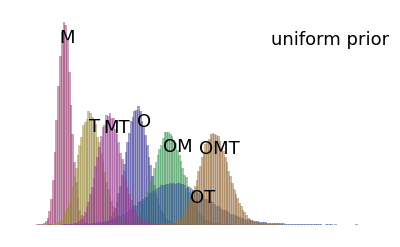

```mathematica
plot=Histogram[T[combodata[[2;;,-7;;-1]]],"FreedmanDiaconis","PDF",ChartLabels->Evaluate[Style[#,18]&/@{"O","M","T","OM","OT","MT","OMT"}],
FrameLabel->{"earth-mover's distance from no-insomnia distribution","density"},ImageSize->a4longside,PlotRange->All,Epilog->Text[Style["uniform prior",18],Scaled[{0.9,0.9}]]]
```

```mathematica
Export["distances_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

distances_symptomcombos_unif.pdf

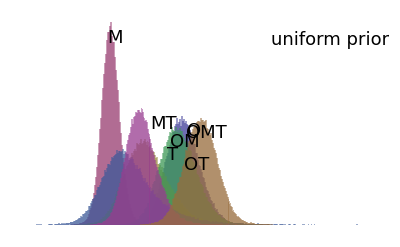

```mathematica
plot=Histogram[T[combodata[[;;,-7-7;;-1-7]]],"FreedmanDiaconis","PDF",ChartLabels->Evaluate[Style[#,18]&/@{"O","M","T","OM","OT","MT","OMT"}],
FrameLabel->{"difference in 3rd moment from no-insomnia distribution","density"},ImageSize->a4longside,PlotRange->All,Epilog->Text[Style["uniform prior",18],Scaled[{0.9,0.9}]]]
```

```mathematica
Export["3rddistances_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

3rddistances_symptomcombos_unif.pdf

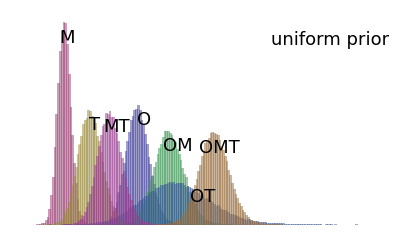

```mathematica
plot=Histogram[T[combodata[[;;,-7-7-7-7;;-1-7-7-7]]],"FreedmanDiaconis","PDF",ChartLabels->Evaluate[Style[#,18]&/@{"O","M","T","OM","OT","MT","OMT"}],
FrameLabel->{"difference in mean from no-insomnia distribution","density"},ImageSize->a4longside,PlotRange->All,Epilog->Text[Style["uniform prior",18],Scaled[{0.9,0.9}]]]
```

```mathematica
Export["meandistances_symptomcombos_unif.pdf",plot,Magnification->1,ImageResolution->400]
```

meandistances_symptomcombos_unif.pdf